# Envariabelanalys Projektuppgift 1.5 hp

## MA2001/MA2049 Envariabelanalys HT21

Rapportversion 1, inlämnad 2022 - 01 - 16

## Grupp

Daniel Bleckert

Erik Knutsson

Vincent Larewall

Linus Frisk

## Uppgifter

### Instruktioner

Varje deluppgift i projektet ska redovisas enligt nedan.

Krav: Filen ska klara “Ctrl-A” + “Shift-return” utan att lämna något felmeddelande.

Handledningar till Mathematica hittar du här: http://dixon.hh.se/mikael/links.shtml

Svensk rättstavning kan väljas i 
Format->Option inspector->Formatting options->Text content options
eller genom att köra:

```mathematica
CurrentValue[EvaluationNotebook[],DefaultNaturalLanguage]="Swedish";
```

Rapporten måste klara “Ctrl-A + shift-return” utan att lämna något felmeddelande!

### 1)

#### Problem

Det första problemet är att detektorkondensatorns märkning är otydlig och därför måste först dess
kapacitans bestämmas. Någon har redan på börjat detta arbete vilket resulterat i mätserien som
finns i filen matserie.dat. Tabellen i filen visar spänningen (V) över kondensatorn som funktion
av tiden (s) då den urladdas genom en resistor på 22 GΩ.
Utnyttja hela mätserien och bestäm:
	(a) Spänningen uC över kondensatorn och strömmen i genom resistorn vid tiden t.
	(b) Kondensatorns kapacitans C0.
	(c) Den tid det tar innan kondensatorns laddning minskat till hälften.
	(d) Effektutvecklingen i resistorn vid tiden t
	(e) Värmeenergin som utvecklas i resistorn under tiden 0 ≤ t ≤ 0.1 s samt totala värmeenergin
		som utvecklats då kondensatorn urladdats helt. Utnyttja resultatet i (d).

#### Lösning

a)  Vi använder oss av ekvationen från föreläsningen Differentialekvationer del 1. Vi löste ekvationen med Mathematicas funktion “DSolve”. Detta gjorde att vi fick fram funktionen för spänningen över kondensatorn. Därefter använde vi oss av “FindFit” och med hjälp av datan från “matserie.dat” så hittade vi lämpliga värden på konstanterna. 
Sedan gjorde vi på motsvarande sätt för strömmen och sedan löste vi ut konstanten för strömmen som är u_0/R.

b) Konstanten i exponenten för båda funktionerna sattes till k och vi kunde därför lösa ut c_0 genom att ställa upp ekvationen C_0 = -1/(R*k)

c) Vi löste differentialekvationen för laddningen(q) som vi fick från föreläsningen “Differentialekvationer del 1” med “DSolve”. Vi löste ut konstanten q_0 genom att ta c_0 * u_0. Sedan ställde vi upp ekvationen “Funktionen för laddningen = hälften av q_0 med avseende på t”. Därefter fick vi ut vilken tid det tar för laddningen att minska till hälften.

d) Eftersom effekt = strömmen i kvadrat × resistansen så har vi ekvationen P = I^2 × R. Därför blir effektutvecklingen i resistorn vid tiden t funktionen för strömmen i kvadrat × resistansen. 

e) Eftersom energin är integralen av effekt så integrerar vi funktionen för effekt med dem tidsgränserna som är angivna i uppgiften. Dessa tidsgränser används som integrationsgränserna.

#### Mathematicakod

```mathematica
Remove["Global`*"];
```

```mathematica
DSolve[u'[t]+ 1/Subscript[RC, 0]*u[t] == 0,u, t]
```

{{u→Function[{t},ⅇ^(-t/RC_0) C[1]]}}

```mathematica
data = Import["http://dixon.hh.se/mikael/teaching/analys/project/matserie.dat", "Table"];
FindFit[data, u0*ⅇ^(t*k), {k, u0}, t]
```

{k→-1.18942,u0→264.9}

```mathematica
k = -1.1894207939837256;
```

```mathematica
R = 22*10^9;
```

```mathematica
Subscript[u, 0] = 264.90048672261605;
```

```mathematica
funk = Subscript[u, 0]*ⅇ^(t*k);
```

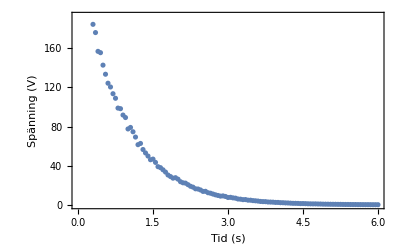

```mathematica
ListPlot[{data}, Frame -> True,  FrameLabel-> {"Tid (s)", "Spänning (V)"}]
```

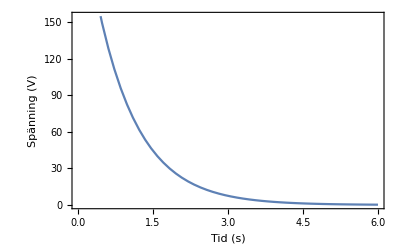

```mathematica
Plot[funk,{t,0,6}, Frame -> True,  FrameLabel-> {"Tid (s)", "Spänning (V)"}]
```

```mathematica
Print["U"]
```

U

```mathematica
DSolve[i'[t]+ 1/Subscript[RC, 0]*i[t] == 0,i, t]
```

{{i→Function[{t},ⅇ^(-t/RC_0) C[1]]}}

```mathematica
Print["i_0 = ",Subscript[u, 0]/(22*10^9)] (* Subscript[i, 0] = Subscript[u, 0]/R*)
```

i_0 = 1.20409×10^-8

```mathematica
Print["i(t) = 264.9/(22*SuperscriptBox[10, 9]) * ⅇ^(-1.1894207939837256*t)"]
```

i(t) = 264.9/(22*SuperscriptBox[10, 9]) * ⅇ^(-1.1894207939837256*t)

```mathematica
Subscript[C, 0] = -1/(R*k);
```

```mathematica
Print["C_0 = ",Subscript[C, 0]=-1/(22*10^9*-1.1894207939837256)]
```

C_0 = 3.82157×10^-11

```mathematica
DSolve[q'[t]+ 1/Subscript[RC, 0]*q[t] == 0,q, t]
```

{{q→Function[{t},ⅇ^(-t/RC_0) C[1]]}}

```mathematica
Print["q_0 = ",Subscript[C, 0]*Subscript[u, 0] ] (* Subscript[q, 0]=Subscript[C, 0]*Subscript[u, 0] *)
```

q_0 = 1.01234×10^-8

```mathematica
Subscript[q, 0]=1.0123356910833625*^-8;
```

```mathematica
qhalf = Subscript[q, 0]/2;
```

```mathematica
Solve[Subscript[q, 0]*ⅇ^(-t/(R*Subscript[C, 0]))==qhalf,t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{t→0.58276}}

```mathematica
Print["P = i^2*R"]
```

P = i^2*R

```mathematica
R = 22*10^9;
Print["P = ",(264.9/(22*10^9) * ⅇ^(-1.1894207939837256*t))^2*R]
∫(264.9/(22*10^9) * ⅇ^(-1.1894207939837256*t))^2* 22*10^9 ⅆt
```

P = 3.18964×10^-6 ⅇ^(-2.37884 t)

-1.34084×10^-6 ⅇ^(-2.37884 t)

```mathematica
Print["E(0.1) = ",Integrate[(264.9/(22*10^9) * ⅇ^(-1.1894207939837256*t))^2* 22*10^9,{t, 0, 0.1}]]
Print["E_tot = ",Integrate[(264.9/(22*10^9) * ⅇ^(-1.1894207939837256*t))^2* 22*10^9,{t, 0, Infinity}]]
```

E(0.1) = 2.83863×10^-7

E_tot = 1.34084×10^-6

#### Slutsatser och resultat

a)
 U_c(t)=264.9*ⅇ^(-1.1894207939837256*t).
i(t)=264.9/(22*10^9) * ⅇ^(-1.1894207939837256*t).

b)
C_0 = 3.82157×10^-11 F.

c)
t = 0.582762 sekunder.

d)
P(t) = 3.18964×10^-6 ⅇ^(-2.37884 t)

e)
E(0.1) = 2.83863×10^-7 J
E_tot= 1.34084×10^-6 J

### 2)

#### Problem

Spänningskällan som används till larmet lämnar en konstant likspänning på 240 V. Ampere-
metern har en utgång som kan kopplas till en sirén och denna utgång aktiveras om strömmen är
över 1.00 μA under minst 250 μs. Tjuvlarmet ska konstrueras så att det löser ut om kapacitansen
förändras med mer än 10%. Tiden det tar för kapacitansen att förändras då ett objekt kommer i
närheten av kondensatorn är i detta sammanhang försumbar.

(a) Förklara hur seriekretsen kan fungera som ett tjuvlarm.
(b) Bestäm de värden på serieresistansen som uppfyller specifikationerna ovan.
	Tips: Mathematica-funktionerna DSolve och NSolve kan användas här.
(c) Förklara vad som händer om man väljer för stor respektive för liten resistans

#### Lösning

a) När en tjuvhand närmar sig kondensatorn ökar kapacitansen. Då börjar det flöda en ström i kretsen och energin kan lagras.
Larmet kommer alltså inte aktiveras på egen hand eftersom kondensatorn själv inte kommer åstadkomma den strömstyrkan som behövs för att larmet ska aktiveras. Det behöver alltså vara något som t.ex en del av tjuvens kropp som börjar närma sig kondensatorn som får kapacitansen att öka. Det behövs dessutom rätt värde på serieresistansen i kretsen för att amperemetern ska nå 1,00μ A under minst 250μs så att sirenen börja tjuta.

b) För att bestämma resistansen i kretsen börjar vi med att derivera lösningen på q(t) som är samma som I(t). Därefter ställer vi upp en ekvation med I(250μs) = 1μA med avseende på resistansen. Därefter får vi ett intervall för resistansen där minsta värdet är 3 MΩ och det högsta är 14 MΩ. För att verifiera att värdet på resistansen är korrekt så plottar vi strömmens funktionsvärde i något av de gränserna på resistansen i tiden 250μs och 1μA i samma graf. Vi ser att funktionerna överlappar varandra, vilket innebär att de har samma värde.

c) Det som händer om man väljer för stor resistans är att strömmen aldrig når över 1μA. Väljer man istället för liten resistans så kommer strömmen att avta för snabbt vilket gör att strömmen inte håller sig över 1μA i minst 250μs.

#### Mathematicakod

```mathematica
Remove["Global`*"]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{r→2.99463×10^6},{r→1.44619×10^7}}

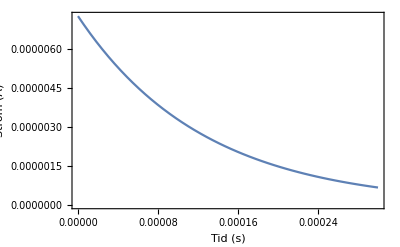

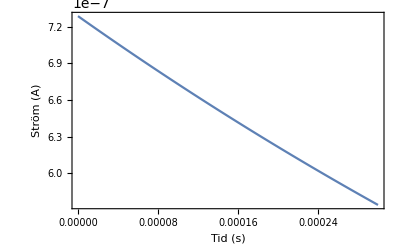

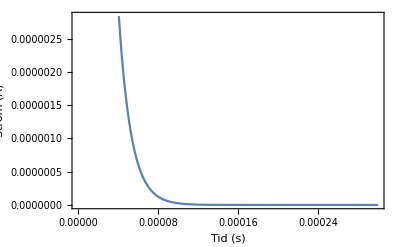

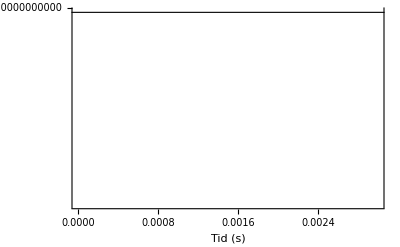

```mathematica
qsolve = DSolve[{q'[t]+q[t]/(r*c)==e/r,q[0]==c0 * e},q[t], t];
D[qsolve,t];
e = 240;
c0 = 3.8215697660963705*^-11;
c = c0 * 1.1;
tmin = 250*10^-6;
imin = 1*10^-6;
Solve[e/r-(e ⅇ^(-tmin/(c r)) (-c+c0+c ⅇ^(tmin/(c r))))/(c r)==imin, r]
Subscript[r, max]=1.44619×10^7;
Subscript[r, min]=2.99463×10^6;
Subscript[r, big] = 2.99462947128288*10^7;
Subscript[r, small] = 2.99462947128288*10^5;
ifunc = e/Subscript[r, min]-(e* ⅇ^(-t/(c* Subscript[r, min])) (-c+c0+c* ⅇ^(t/(c *Subscript[r, min]))))/(c* Subscript[r, min]);
ifunctoobig = e/Subscript[r, big]-(e* ⅇ^(-t/(c* Subscript[r, big])) (-c+c0+c* ⅇ^(t/(c *Subscript[r, big]))))/(c* Subscript[r, big]);
ifunctoosmall =  e/Subscript[r, small]-(e* ⅇ^(-t/(c* Subscript[r, small])) (-c+c0+c* ⅇ^(t/(c *Subscript[r, small]))))/(c* Subscript[r, small]);
Plot[ifunc,{t,0,300*10^-6}, Frame -> True,  FrameLabel-> {"Tid (s)", "Ström (A)"}]
Plot[ifunctoobig,{t,0,300*10^-6}, Frame -> True,  FrameLabel-> {"Tid (s)", "Ström (A)"}]
Plot[ifunctoosmall,{t,0,300*10^-6}, Frame -> True,  FrameLabel-> {"Tid (s)", "Ström (A)"}]
Plot[{e/(1.4461910152141402*10^7)-(e* ⅇ^(-tmin/(c*1.4461910152141402*10^7)) (-c+c0+c* ⅇ^(tmin/(c *1.4461910152141402*10^7))))/(c* 1.4461910152141402*10^7),1*10^-6},{t,0,300*10^-5},Frame -> True,  FrameLabel-> {"Tid (s)", "Ström (A)"}]
```

#### Slutsatser och resultat

a) Se lösning ovan.
b) r_min=2.99463×10^6 ≤ R ≤ r_max=1.44619×10^7
c) Se lösning ovan.

### 3)

#### Problem

Antag nu att man vill öka känsligheten på larmet.
a) Hur små kapacitansförändringar kan man mäta med ovanstående utrustning?
b) Vilken spänning krävs om larmet ska kunna detektera kapacitansförändringar ner till 5% ?

#### Lösning

a) Det första vi gör är att bestämma den resistans som ger högst ström efter 250μs. Sedan ställer vi upp en ekvation där vi löser ut förändringsfaktorn för kapacitansen genom att ställa upp funktionen för ström i tiden 250μs = 1μA. Därefter får vi ut förändringsfaktorn som är ungefär 1,07 vilket innebär att vår krets kan mäta kapacitansförändringar på minst 7%.

b) Vi ställer upp samma ekvation som i 3a men vi sätter förändringsfaktorn till 1,05 och vi löser ut “e” som är spänningen.

#### Mathematicakod

```mathematica
Remove["Global`*"]
```

```mathematica
Subscript[r, max]=1.44619×10^7;
Subscript[r, min]=2.99463×10^6;
r0 = 5.692908246301442*10^6;
e = 240;
c0 = 3.8215697660963705*^-11;
c = 1.1*c0;
tmin = 250*10^-6;
imin = 1*10^-6;

Print["r_max = ",FindMaximum[e/r-(e ⅇ^(-tmin/(c r)) (-c+c0+c ⅇ^(tmin/(c r))))/(c r),{r, Subscript[r, min],Subscript[r, max]}]]
Clear[c];
r0 = 5.692908246301442*10^6;
Solve[e/r0-(e *ⅇ^(-tmin/(c*c0 *r0)) *(-(c*c0)+c0+c*c0 *ⅇ^(tmin/(c*c0* r0))))/(c*c0 *r0)==imin, c]
kap = 1.0742658417659676-1;

Print["Lägsta kapacitansförändring: ", kap*100," %"]
Clear[e]
c = 1.05;
Solve[e/r0-(e *ⅇ^(-tmin/(c*c0 *r0)) *(-(c*c0)+c0+c*c0 *ⅇ^(tmin/(c*c0* r0))))/(c*c0 *r0)==imin, e]
kap5 = 357.14442973261606;
Print["Spänning som krävs för 5 % kapacitansförändring: ", kap5, " V"]
```

r_max = {1.34834×10^-6,{r→5.69291×10^6}}

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{c→1.07427}}

Lägsta kapacitansförändring: 7.42658 %

{{e→357.144}}

Spänning som krävs för 5 % kapacitansförändring: 357.144 V

#### Slutsatser och resultat

a) 7,4%
b) 357 V

## Referenser

Här anges vilka källor som utnyttjats och som refereras till i rapporten. Ex:

[1] Projektuppgift 1.5 hp,  http://dixon.hh.se/mikael/teaching/analys/project/projekt_ma2001ht21.pdf

[2] Presentation differentialekvationer del 1,  http://dixon.hh.se/mikael/teaching/analys/lectures/differentialekv1.pdf